```mathematica
NN = 3;
mm  = 1.0;


M1 = mm ( ⅇ^(2 π ⅈ / NN) - 1. );
M2  = mm( ⅇ^(4 π ⅈ / NN) - 1. );
M = Abs[M1];
μ1  = M1/(2 M);
μ2  =  M2/(2 M);
ϕ1[s_] := ⅇ^(s / 2)
χ[s_] := 1 + ϕ1[s] ϕ1[s]
f[s_] := (ϕ1[s])^2/χ[s]
λ = (- √3)/4;
eq := {   -  ϕ''[s]      +     f[s] ϕ'[s]      +      1/4 ϕ[s]    -     1/8 f[s] ϕ[s]    +     1/4 f[s]  (ⅇ^s - 1)/χ[s] ϕ[s]      ==    λ ϕ[s]  }
```

```mathematica
Lmass = √(1/4 - λ);
Lϕ[s_] := ⅇ^(Lmass s)
Rmass = √(3/8 - λ);
κ = 1/2 - √(5/8 - λ);
Rϕ[s_] := ⅇ^(κ s)
```

100

{{ϕ→InterpolatingFunction[{{-100.,100.}},<>]}}

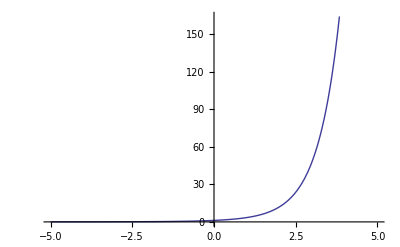

```mathematica
S = 100
Φsolve = NDSolve[ { eq, ϕ[-10] == Lϕ[-10] , ϕ'[-10] ==  1.00000935Lmass Lϕ[-10] }, { ϕ }, {s, -S, S} ]
Plot[ Evaluate[   ϕ[s] /. Φsolve ], {s, -5, 5} ]
```

```mathematica
Evaluate[   ϕ[-50] /. Φsolve ]
```

{-167.788}

100

{{ϕ→InterpolatingFunction[{{-100.,100.}},<>]}}

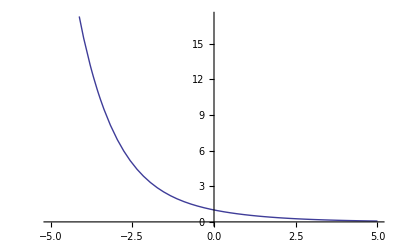

```mathematica
S = 100
Φsolve = NDSolve[ { eq, ϕ[10] == Rϕ[10] , ϕ'[10] ==  0.9999κ Rϕ[10] }, { ϕ }, {s, -S, S} ]
Plot[ Evaluate[   ϕ[s] /. Φsolve ], {s, -5, 5} ]
```

```mathematica
Evaluate[   ϕ[50] /. Φsolve ]
```

{4.53927×10^19}